```mathematica
Clear[g1]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}]
g1[n_,k_] := g1[n,k]=Sum[ dz[a^2,2]g1[Floor[n/a],k-1],{a,1,n}]
g1[n_,0]:=UnitStep[n-1]
g2[n_,k_] := Sum[ (-1)^(k-j) bin[k,j] g1[n,j],{j,0,k}]
lg[n_] := Sum[ (-1)^(k+1)/k g2[n,k],{k,1,Log2@n}]
kk[n_]:=kk[n]=FullSimplify[MangoldtLambda[n]/Log[n]]
pr[n_,s_] :=Sum[ kk[j] j^s,{j,2,n}]
ts[n_] := 3 pr[n,0] - pr[ n^(1/2),0]
```

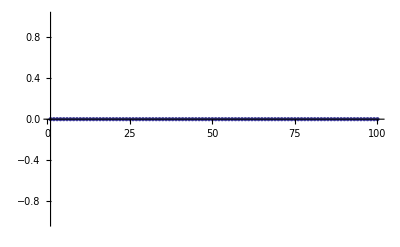

```mathematica
DiscretePlot[ lg[n] ,{n,1,100}]
```

```mathematica
Clear[g1]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}]
g1[n_,k_] := g1[n,k]=Sum[ dz[a,2] g1[Floor[n/a],k-1],{a,1,n}]
g1[n_,0]:=UnitStep[n-1]
g2[n_,k_] := Sum[ (-1)^(k-j) bin[k,j] g1[n,j],{j,0,k}]
lg[n_] := Sum[ (-1)^(k+1)/k g2[n,k],{k,1,Log2@n}]
kk[n_]:=kk[n]=FullSimplify[MangoldtLambda[n]/Log[n]]
pr[n_,s_] :=Sum[ kk[j] j^s,{j,2,n}]
ts[n_] := 3 pr[n,0] - pr[ n^(1/2),0]
```

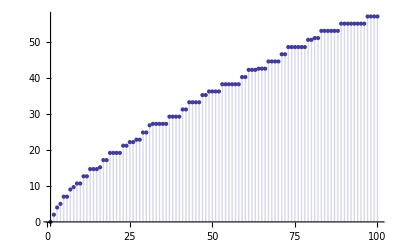

```mathematica
DiscretePlot[ lg[n] ,{n,1,100}]
```